# HW #2: Section 1.2 # 20, 22, 30 Section 3.1 # 1, 2, 8

## Cole Pendergraft ID# 951544267

## 1.2 #20

What is the fifth term in the Taylor series of (1 - (2h))^(1/2)?

We can expand out this Taylor series to five terms using the series command.

```mathematica
Normal[Series[Sqrt[1-2h], {h, 0, 4}]]
```

1-h-h^2/2-h^3/2-(5 h^4)/8

The fifth term in the Taylor series of (1 - (2h))^(1/2) is -(5 h^4)/8.

## 1.2 #22

Show how p(x) = 6(x + 3) + 9(x (+3))^5 - 5(x + (3))^8 - (x + (3))^11 can be efficiently evaluated.

The method that first comes to mind for evaluating this polynomial is to use the grouping method to factor out the polynomial.

I struggled to determine how to do this factoring process in Mathematica, and ultimately was unable to do so. Therefore, I’ve done the factoring process by hand and provided it below, and used Mathematica modules for the simpler steps.

Moving from right to left, we can start by extracting -(x+3)^8 from -5(x+3)^8 - (x+3)^11.

Now we have p(x) = 6(x+3) + 9(x+3)^5 - (x+3)^8[5 + (x + 3)^3].

Next, we can extract (x + 3)^5 from 9(x+3)^5 - (x+3)^8[5 + (x + 3)^3].

This leaves us with p(x) = 6(x+3) + (x+3)^5[9 - (x+3)^3[5 + (x+3)^3]].

Finally, we can extract a single (x+3) from 6(x+3) + (x+3)^5[9 - (x+3)^3[5 + (x+3)^3]].

This leaves us with our final factored equation p(x) = (x+3)[6+(x+3)^4[9 - (x+3)^3[5 + (x+3)^3]]].

So now we can calculate roots by isolating single terms, and I am going to demonstrate this by finding the roots of this polynomial. We have roots where (x+3) = 0, roots where 6+(x+3)^4 = 0, roots where 9 - (x + 3)^3 = 0, and roots where 5 + (x+3)^3 = 0.

Therefore, we can finish this evaluation by using the Solve module on each of these individual terms and determine the values of x that make each term 0.

```mathematica
Solve[(x + 3) == 0, x]
Solve[ 6 + (x+3)^4 == 0, x]
Solve[9 - (x+3)^3 == 0, x]
Solve[5 + (x+3)^3 == 0, x]
```

{{x→-3}}

{{x→-3-(-6)^(1/4)},{x→-3+(-6)^(1/4)},{x→-3-(-1)^(3/4) 6^(1/4)},{x→-3+(-1)^(3/4) 6^(1/4)}}

{{x→Root-0.920Root[18+27 #1+9 #1^2+#1^3&,1]-0.919916176948096},{x→Root-4.04-1.80 ⅈRoot[18+27 #1+9 #1^2+#1^3&,2]-4.040041911525952},{x→Root-4.04+1.80 ⅈRoot[18+27 #1+9 #1^2+#1^3&,3]-4.040041911525952}}

{{x→Root-4.71Root[32+27 #1+9 #1^2+#1^3&,1]-4.709975946676697},{x→Root-2.15-1.48 ⅈRoot[32+27 #1+9 #1^2+#1^3&,2]-2.145012026661651},{x→Root-2.15+1.48 ⅈRoot[32+27 #1+9 #1^2+#1^3&,3]-2.145012026661651}}

And there we have all 11 of our roots, the function evaluates to 0 where x is equivalent to all the above values. 

Now suppose we wanted to evaluate for some value other than x = 0, now that we have this factored system we can do this with relative ease.

```mathematica
Clear[g];
g[x_]=(x + 3)(6 + (x+3)^4(9 - (x+3)^3(5 + (x+3)^3)))
g[2]
```

(3+x) (6+(3+x)^4 (9-(3+x)^3 (5+(3+x)^3)))

-50753095

## 1.2 #30

Use Taylor’s Theorem to find a linear function that approximates cos x best in the vicinity of x = 5π/6.

Firstly, I am going to create a simple Taylor series for f(x+h). We know that the equation for the Taylor series is f(x+h) = (Σ_(k = 0))^n (f^(k)(x))/(k!) h^k + E_(n + 1) . I am going to create this Taylor Series by hand out to 4 terms, and then proceed to calculate the error on my approximation. The more terms that the Taylor Series goes out to, the better the approximation.

```mathematica
f[x_] = Cos[x];
Simplify[f[x]+(f'[x]*h )+ ((1/2)f''[x]*h^2) +((1/6)f'''[x]*h^3)]
f''''[x]
```

1/6 (-3 (-2+h^2) Cos[x]+h (-6+h^2) Sin[x])

Cos[x]

Of course, since we don’t have any provided values for h, we can’t really do any actual computing, but we can represent things in general terms and analyze things that way. 

We know that the error term is E_(n + 1) = (Σ_(k = 0))^n (f^(n+1)(ξ))/((n+1)!) h^(n+1), so:

```mathematica
E4 = ((Cos[ξ])/(4!)) * h^4
```

1/24 h^4 Cos[ξ]

We know that ξ > 1, which means that Cos(ξ) < 1, and finally that tells us that 1/24 h^4 Cos[ξ]< 1/24 h^4. This implies that our error is no more than 1/24 h^4. Now if we had values for h, we could compute this problem and determine just how close our approximation gets to the correct value.

## 3.0 #1

Find where the graphs of y = 3x and y = e^x intersect by finding roots of e^x - 3x = 0 correct to four decimal digits.

Below is the Newton algorithm provided in Lab4:

```mathematica
Newton[f_,p_,max_,delta_]:=Module[{p0,p1,Y0,DY0,dp}, (*input function, first guess, # of iterations, and accuracy*)
p0=p; (*Module vars: current estimate, next estimate, y-value, slope, and distance "improved"*)
For[i=0,i<max,i++,
Y0=N[f/.x->p0]; (*Numerical current y-value*)
DY0 = N[D[f,x]/.x->p0];(*Numerical current slope*)
If[DY0==0,Print["Found a horizontal tangent at x =", p0];Return[p0]];
p1= p0-Y0/DY0;(*Compute next iteration*)
dp=Abs[p0-p1];(*Keep track of how much we moved this step*)
 Print["p = ",N[p1],   "\t  |dp| <= ",N[dp],"\t iteration: ",i];
If[dp<delta,Print["Accuracy attained since delta is", delta," and dp is ",dp];Return[p1]];
p0=p1; (*Make new estimate the current estimate and repeat*)
];
Return[p0];
]
```

I am going to iterate through above code until I produce e^x - 3x = 0 correct to four decimal places. I can do this by setting my delta_ value as .5*10^(-4), which will tell the program to stop iterating once the first four decimal places are locked in and unchanging.

```mathematica
f[x_] = E^x - 3x;
Newton[f[x], 2, 10, .5*10^(-4)]
```

p = 1.68352	  |dp| <= 0.316482	 iteration: 0

p = 1.54348	  |dp| <= 0.140036	 iteration: 1

p = 1.51349	  |dp| <= 0.0299933	 iteration: 2

p = 1.51214	  |dp| <= 0.00135137	 iteration: 3

p = 1.51213	  |dp| <= 2.69846×10^-6	 iteration: 4

Accuracy attained since delta is0.00005 and dp is 2.69846×10^-6

1.51213

So we pretty rapidly were able to calculate this intersection point. We now know that y = 3x and y = E^x intersect somewhere close to 1.51213. We can’t say for sure that the intersection point is exactly 1.51213 as we only iterated with a specificity of 4 decimal digits.

## 3.1 #2

Give a graphical demonstration that the equation tan(x) = x has infinitely many roots. Determine one root precisely and another approximately by using a graph.

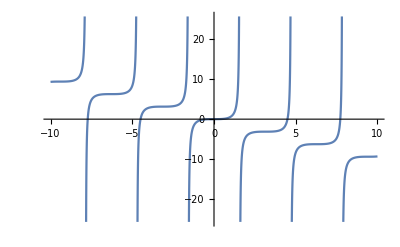

```mathematica
Plot[Tan[x] == x, {x, -10, 10}]
```

How can we determine if this graph has infinitely many roots? Well we can first set tan(x) = 0 and then expand tan(x):

tan(x) = (sin(x))/(cos(x))= 0

Now we know we have (sin(x))/(cos(x)) = 0, and the only necessity to make that happen is that sin(x) = 0, and cos(x) != 0.

If sin(x) = 0, then we know that x = nπ, where n is an integer, because any integer multiple of PI will make sin go to 0. So what this tells us is that if tan(x) = 0, x is some integer multiple of pi, of which there is an infinite amount due to the infinite number of integers. Therefore there are infinitely many solutions for this problem.

Looking at this graph we can attempt to approximate a couple of roots by sight without calculation. It seems like there are intersections at +4.5, -4.5, +7.75, and -7.75.

We can also compute some roots precisely. We know that x will be a root wherever Tan(x) = 0 while Tan(x) = x still remains true. One obvious precise root would be 0, as if we set x=0, we get Tan(0) = 0, but at the same time we still have Tan(x) = x so we haven’t violated any conditions.

## 3.1 #8

If a = 0.1 and b = 1.0, how many steps of the bisection method are needed to determine the root with an error of at most 0.5 * 10^(-8).
The beauty of the Bisection method is that it is so simplistic that the input function is irrelevant when determining the number of steps the method needs to take. What this means is I can select any function to calculate for as long as I specify a = 0.1, b = 1.0, and error = 0.5*10^(-8). Furthermore, this code displays the error bounds at each iteration, so we can simply vary the max_ value until we have produced an error bound <= 0.5*10^(-8).

Below is the Bisection algorithm provided in Lab3:

```mathematica
Bisection[ {a0_,b0_}, Max_]:=(*Assumes a pre-defined function f, input interval and number of iterations *)
Module[{a,b,c,Ya,Yb,Yc,k,dx, dp},
  a = N[a0]; b = N[b0];
  k = 0; Ya = f[a]; Yb = f[b];
If[Ya*Yb>0,Print[ Ya," and ", Yb, " have the same sign, so no guaranteed root."]; Return[]]; (*Make sure the user has defined an appropriate interval *)
If[Ya ==0,Print[ a, " is an exact root!"]; Return[a]]; (*Maybe the user imputs a root *)
If[Yb ==0,Print[ b, " is an exact root!"]; Return[b]];
  For[k=0, k < Max, k++, (*Run this for loop Max times *)
    c  = (a+b)/2;
    Yc = f[c];
If[Yc ==0,Print[ c, " is an exact root!"]; Return[c]];
    dx = b-a;
    Print["k = ",k,"\t    c = ",N[c],"\t  error <= ",N[dx]];
If [Sqrt[2] - c == 0.5*10^(-8)];
Return[c, "Reached number of steps to compute within error"];
      If[Yb*Yc>0, b=c;  Yb=Yc,(* If the function doesn't change signs in (b,c), we use the interval (a,c) *)
 a=c;   Ya=Yc]; ]; (* Otherwise we use (b,c) *)
Return[c]];
```

In order to use the Bisection algorithm, we need to solve for some value between 0.1 and 1.0, like √0.5. This means f(x) = x^2 - 0.5.

```mathematica
f[x_] = x^2 - 0.5;
Bisection[{0.1, 1.0}, 28]
```

k = 0	    c = 0.55	  error <= 0.9

k = 1	    c = 0.775	  error <= 0.45

k = 2	    c = 0.6625	  error <= 0.225

k = 3	    c = 0.71875	  error <= 0.1125

k = 4	    c = 0.690625	  error <= 0.05625

k = 5	    c = 0.704688	  error <= 0.028125

k = 6	    c = 0.711719	  error <= 0.0140625

k = 7	    c = 0.708203	  error <= 0.00703125

k = 8	    c = 0.706445	  error <= 0.00351563

k = 9	    c = 0.707324	  error <= 0.00175781

k = 10	    c = 0.706885	  error <= 0.000878906

k = 11	    c = 0.707104	  error <= 0.000439453

k = 12	    c = 0.707214	  error <= 0.000219727

k = 13	    c = 0.707159	  error <= 0.000109863

k = 14	    c = 0.707132	  error <= 0.0000549316

k = 15	    c = 0.707118	  error <= 0.0000274658

k = 16	    c = 0.707111	  error <= 0.0000137329

k = 17	    c = 0.707108	  error <= 6.86646×10^-6

k = 18	    c = 0.707106	  error <= 3.43323×10^-6

k = 19	    c = 0.707107	  error <= 1.71661×10^-6

k = 20	    c = 0.707107	  error <= 8.58307×10^-7

k = 21	    c = 0.707107	  error <= 4.29153×10^-7

k = 22	    c = 0.707107	  error <= 2.14577×10^-7

k = 23	    c = 0.707107	  error <= 1.07288×10^-7

k = 24	    c = 0.707107	  error <= 5.36442×10^-8

k = 25	    c = 0.707107	  error <= 2.68221×10^-8

k = 26	    c = 0.707107	  error <= 1.3411×10^-8

k = 27	    c = 0.707107	  error <= 6.70552×10^-9

0.707107

We can see that once we reach k = 27 we have an error within our specified margins, we can adjust 6.70552*10^(-9) to be 0.670552*10^(-8), and clearly we have 0.5*10^(-8) < 0.670552*10^(-8), meaning that we have reached acceptable error levels after 28 iterations.